# FindRandomHexagonalGridMazeSolution

Find the solution to a random hexagonal grid maze

## Definition

```mathematica
PositiveIntegerQ//ClearAll
```

```mathematica
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
PositiveIntegerQ::usage="PositiveIntegerQ[n] returns True when n is a strictly positive integer.";
```

```mathematica
ClearAll[FindRandomHexagonalGridMazeSolution]
```

```mathematica
FindRandomHexagonalGridMazeSolution::usage="FindRandomHexagonalGridMazeSolution[{StyleBox[\"m\", \"TI\"],StyleBox[\"n\", \"TI\"]}] finds a solution and other data for a random hexagonal grid maze of size StyleBox[\"m\", \"TI\"] by StyleBox[\"n\", \"TI\"].";
```

```mathematica
FindRandomHexagonalGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges. This is known as the trivial graph, the singleton, or the unit graph.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=ResourceFunction["HexagonalGridGraph"][{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=Last@VertexList[m] (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->Iconize[shortestPath,"shortest-path"],"distance"->GraphDistance[m,start,end],"shortest-path-subgraph"->shortestPathSubgraph|>](*some ideas for other properties to add include deadends.*)
```

## Documentation

### Usage

FindRandomHexagonalGridMazeSolution[{m,n}]

finds a solution and other data for a random hexagonal grid maze of size m by n.

### Details & Options

There are three ways to tile the plane: with squares, which GridGraph does and the ResourceFunction FindRandomGridMazeSolution will make a maze for, with hexagons which the ResourceFunction HexagonalGridGraph does and FindRandomHexagonalGridMazeSolution will make a maze for, and with triangles which TriangularGridGraph does and the ResourceFunction FindRandomTriangularGridMazeSolution I am working on will make a maze for.

The shortest path data is iconized because the shortest-path might be very large. To get the data, use First on IconizedObject. You can also click the plus button and click Uniconize.

## Examples

### Basic Examples

Make a random 7 by 7 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{7,7}]
```

-Graphics-

Make a random 10 by 10 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{10,10}]
```

-Graphics-

Make a random 15 by 15 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{15,15}]
```

-Graphics-

### Scope

Make a random rectangular 8 by 21 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{8,21}]
```

-Graphics-

Make a random rectangular 21 by 8 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{21,8}]
```

-Graphics-

### Options

### Applications

Make a random 20 by 20 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{20,20}]
```

-Graphics-

Make a random 25 by 25 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{25,25}]
```

-Graphics-

Make a random 30 by 30 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{30,30}]
```

-Graphics-

Make a random 35 by 35 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{35,35}]
```

-Graphics-

Make a random 40 by 40 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{40,40}]
```

-Graphics-

Make a random 45 by 45 hexagonal grid maze:

```mathematica
EchoTiming[FindRandomHexagonalGridMazeSolution[{45,45}]]
```

1.57894

-Graphics-

Make a random 50 by 50 hexagonal grid maze:

```mathematica
FindRandomHexagonalGridMazeSolution[{50,50}]
```

-Graphics-

Make a random 55 by 55 hexagonal grid maze:

```mathematica
EchoTiming[FindRandomHexagonalGridMazeSolution[{55,55}]]
```

3.02925

-Graphics-

Make a random 60 by 60 hexagonal grid maze:

```mathematica
EchoTiming[FindRandomHexagonalGridMazeSolution[{60,60}]]
```

4.67228

-Graphics-

Make a random 65 by 65 hexagonal grid maze:

```mathematica
EchoTiming[FindRandomHexagonalGridMazeSolution[{65,65}]]
```

5.60643

-Graphics-

Make a random 70 by 70 hexagonal grid maze. Notice a visualization for maze and solved-maze is not available, but the shortest-path subgraph visualization is available.:

```mathematica
EchoTiming[FindRandomHexagonalGridMazeSolution[{70,70}]]
```

7.76708

-Graphics-

Analyze the output graph to find the dead-ends with graph periphery:

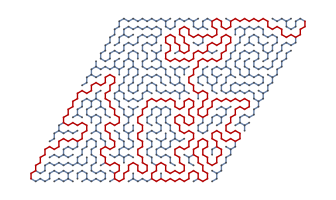

```mathematica
maze=FindRandomHexagonalGridMazeSolution[{20,20}]["solved-maze"]
```

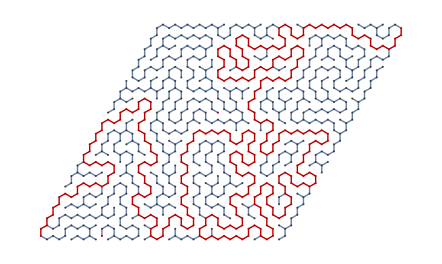

```mathematica
HighlightGraph[maze,GraphPeriphery[maze]]
```

### Properties and Relations

To get the data in Iconized Object, use First:

```mathematica
FindRandomHexagonalGridMazeSolution[{10,10}]["shortest-path"]
```

-Graphics-

```mathematica
FullForm[FindRandomHexagonalGridMazeSolution[{10,10}]["shortest-path"]]
```

IconizedObject[List[1,2,4,7,5,9,14,15,21,22,29,30,38,47,46,37,36,28,27,35,44,54,65,77,88,99,110,111,100,89,78,66,55,56,67,79,90,101,112,123,122,133,132,143,154,165,176,177,187,188,197,198,206,207,214,215,208,209,216,222,227,228,223,217,210,202,193,183,182,171,160,161,172,173,184,185,174,175,186,196,195,204,212,219,225,226,231,235,238,240],"shortest-path",Rule[Method,Automatic]]

```mathematica
First[FindRandomHexagonalGridMazeSolution[{10,10}]["shortest-path"]]
```

{1,2,4,6,8,11,13,17,19,24,26,32,34,41,43,52,50,42,40,49,59,70,69,58,57,47,38,30,29,22,21,28,36,45,55,56,67,68,80,91,102,113,112,123,134,145,144,155,166,167,178,179,168,157,146,147,158,169,180,190,189,198,206,207,214,215,221,222,216,217,223,228,232,233,236,237,239,240}

The data is iconized because the shortest-path might be very large. You can also click the plus button and click Uniconize:

-Graphics-

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Mazes

Graphs

Geometry

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

FindShortestPath

DepthFirstScan

BreadthFirstScan

### Related Resource Objects

RandomMaze

If the next two ResourceFunctions are published, I would like to include them here. Is there a way to futurize the next two cells?

FindRandomGridMazeSolution

FindRandomTriangularMazeSolution

### Source/Reference Citation

I got the idea from the documentation page for FindShortestPath's Application section. I used the ResourceFunction HexagonalGridGraph.

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

```mathematica
?FindRandomHexagonalGridMazeSolution
```

```mathematica
??FindRandomHexagonalGridMazeSolution
```

```mathematica
Information[FindRandomHexagonalGridMazeSolution]
```

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.